## Init

```mathematica
NilsSolToMySol[nilssol_List, mval_Integer, nval_Integer, spin_?NumericQ, pol_Integer]:=
Block[{anglcoeffs, anglfunc, anglfunctmp,μNv, ν,ω,rsol, frobeniusexp},
anglcoeffs = nilssol[[1]][[All,2]];
anglfunctmp = (nilssol[[2]]/.QNMcode`θ->θ);
anglfunc = {θ}|->anglfunctmp//Evaluate;
μNv = nilssol[[3]];
ν = (QNMcode`rν+I*QNMcode`iν)/.nilssol[[4]];
ω = nilssol[[5]];
rsol =( QNMcode`R/.nilssol[[6]]);
frobeniusexp = nilssol[[7]];
<|"Parameters"-><|"m"->mval, "n"->nval, "χ"->spin, "s"->pol, "μNv"->μNv|>, "Solution"-><|"R"->rsol, "S"->anglfunc, "Scoeffs"->anglcoeffs, "ν"->ν, "ω"->ω|>|>
]
$root = NotebookDirectory[];
SetDirectory[$root];
$FKKSRoot = $root<>"../../../";
Import[$FKKSRoot<>"Packages/HelperFunctions.wl"]
```

## QNM Evaluator

```mathematica
Import[$root<>"nonR_master.wl"]
```

## Teukolsky Evaluator

```mathematica
<<HelperFunctions.wl
<<BHEvol.m
<<VectorFieldNorm.m
<<SpinWeightedSpheroidalHarmonics.m
<<RenormalizedAngularMomentum.m
<<MSTformalism.m
<<WeylPsi4.m
<<TeukolskyT.m
<<TeuInter.wl
```

```mathematica
Do[TeuCode[1,0,9/10,i,1], {i,0.2,0.2, 0.05}]//Timing
TeuInterEnv`out10["Derived"]["NormalizedEinf"]
```

Data import: 
	 input mass: 0.20000000000000001110223024625156540424`25.
	 data index: 78
	 mass: 0.19922480620155036401541792654955592097`25.
	 BH Spin: 0.9`25.
	 Mode: 1
	 Overtone: 0
	 Frequency: 0.19489102134649698735086664281854121871`25.150514997606326 + 6.28263685790686499826270660273462`20.65886512385594*^-6*I
	 Eigenvalue: -0.23985781749920411091005578835425024371`25. - 4.1630187909422350415196654922262870877838337472347211`25.*^-6*I

Radsol[2]: 1.44677154587372820071888127513885657087`24.286765205539748 - 1.1754426414705508432784313908349459107`24.33601286590219*I

Angsol[2]: -3.14158886189341326353429446454966368216`25.150300435764304 + 2.791964156414039873191680485246`17.09927517804315*^-8*I

precision: 25

rplus = 1.435889894354067355223698

rstart = 1.445889894354067355223698

epsilonr = 0.006964322291925094379954

rstop = 1496.999999999999833466546

r glue = 179.64

Interpolation: Start.

rmesh = 199

Thetamesh = 49

ThetaStart = 0.007767974743979812191074785

ThetaStop = 3.135539638126066286361038

Exponential extension: Start.

Solution at horizon: Test:

Rad[rtst] = -0.1899423174401339761138 - 0.99646021689914874020482 I

Exponential extension: Done!

Generating Interpolating functions for A_μ

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 1

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

Data produced for: 2

xAct`xTensor`PrintAsCharacter::argx: xAct`xTensor`PrintAsCharacter called with 0 arguments; 1 argument is expected.

General::stop: Further output of xAct`xTensor`PrintAsCharacter::argx will be suppressed during this calculation.

Data produced for: 3

Data produced for: 4

Interpolation: Done.

Adownvector[0,2,2,2] = {-0.685124, -0.398823, 0.55195, 5.1829}

Massnormalization: Start.

Tuptdownt test = -0.379182774277246892324910731986

sqrtmg test = 3.76474079784964483565743350856

rplus = 1.435889894354067355223698

rintstart = 1.44847914847200920362979559286

epsilonrint = 0.008767562309229220612865

rintstop = 1534.76461540120323621541676398

thetastart = 0.007767974743979812191074785

thetastop = 3.135539638126066286361038

massNorm obtained: 27875.7848900512

Anorm obtained: 0.0015392872931056650251

Massnormalization: Done.

FindMaximum::nrnum: The function value 0.+0.0000171353 ⅈ is not a real number at {TeuInterEnv`r,TeuInterEnv`ϕ} = {1.44589,2.61306}.

Beginning Tlmω calculation

Subscript[T, μν] test: {{1.4832398155456616*^-7, 2.991092996182922*^-7, -6.632273420865614*^-8, -3.125577506615326*^-7}, {2.991092996182922*^-7, -2.968698448180298*^-6, 6.98220689833301*^-7, -2.091710053841003*^-6}, {-6.632273420865614*^-8, 6.98220689833301*^-7, 1.2121518082321833*^-6, 8.095406284734485*^-7}, {-3.125577506615326*^-7, -2.091710053841003*^-6, 8.095406284734485*^-7, 2.7218326113722157*^-6}}

TnnExpl Test: 2.4813927057628376*^-8

rrange: {1.44588989435406735522369819838596156591`25., 1.44596452747132953327789002268846137768`25., 1.44628793764613230484605459466596056202`25.} ...

θrange: {0.00776797474397981219107478523255849723`25., 0.0716000495068795361537270913018170288`25., 0.13543212426977926011637939737107556038`25.} ...

---------------------------------------------------------------------

Generating: Tnn...

Generating: Tmn...

Generating: Tmm...

Generating: Done.

---------------------------------------------------------------------

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 2.97153465713523525063053

Generating: Interpolation data...

Generating: Tlmω.

Generating: Spheroidal harmonic for (s=-2,χ,Re(ω_Teu)).

Eigenvalues of SWSH: 9.48205700278135900355012

Generating: Interpolation data...

LinkObject::linkd: Unable to communicate with closed link LinkObject[/mnt/Data_Volume/Computer_Programs/Wolfram/Mathematica/13.1/Executables/wolfram -noinit -subkernel -wstp,753,4].

KernelObject::rdead: Subkernel connected through … appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {371} assigned to ….

LaunchKernels::final: Cloning kernel … failed.

Generating: Tlmω.

Generating: Done.

---------------------------------------------------------------------

MST Solution (l=2, j=2)--------------------------------------

νsol[1]: 1.5`20. + 1.99432859529230066542027088871691375971`20.*I

1.5614023172123221439

νsol[2,2]: 1.53053752705961204054851372021027345917`20.

AlmSWSH: 2.97153465713523525063052659096781487157`20.

λ_swsh: 1.69138263649325455354904115278665825155`19.755256953021902

Power::infy: Infinite expression 1/(0``-3.061563787020192+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.5151086913668182+0. ⅈ) encountered.

Power::infy: Infinite expression 1/(0``-0.5145715764502881+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Divide::infy: Infinite expression (0.001+0. ⅈ)/0. encountered.

λ_(swsh,  MSTpackage): 1.6913826364932545

Rnumerical[2]: 0.242822 - 0.0473922 I

SolR[2]: -0.0977708403994877322841354497527133700651508218964936738417304150 + 0.1474488010188660171919563001000932673908466808300661102232943575 I

Coeff: {PrivateMST`κ -> -0.7807382284022634 + 2.*I, PrivateMST`c1 -> 2.1585460928534914 - 0.11701476403387957*I, PrivateMST`c2 -> 0.8107342130428938 - 0.21140161915221617*I}

R0: -1.126334828468860021749125403400209932399914640308`20.082985350524517*^-10 - 6.80262838548549707064314994342771693644369038581`19.863994583907193*^-11*I

dR0: -0.00001721591254449799504795323315802049`19.935413950148693 - 0.00002239913667039433815570842591819993`20.04971518198983*I

norm: 0.215836842161257369543392314881202764809131622314453125`100.14178049827913 + 0.0437269637572537117620186108979396522045135498046875`99.44840424247474*I

eqset: {(-1.6913826364932545 - (3.11825634154395179761386628509665949934`25.150514997606326*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -1.126334828468860021749125403400209932399914640308`20.082985350524517*^-10 - 6.80262838548549707064314994342771693644369038581`19.863994583907193*^-11*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001721591254449799504795323315802049`19.935413950148693 - 0.00002239913667039433815570842591819993`20.04971518198983*I}

MST Solution (l=3, j=2)--------------------------------------

νsol[1]: 2.5`20. + 2.30268505469030770882454817183315753937`20.*I

2.8159700869309234328

νsol[3,2]: 2.81610951672825715568935567341688242781`20.

AlmSWSH: 9.48205700278135900355012204225029675709`20.

λ_swsh: 7.50029730529198915200551668992239174972`19.89817407880767

λ_(swsh,  MSTpackage): 8.201904982139379

Rnumerical[2]: 1.91517 - 0.959872 I

SolR[2]: -0.05158599851218665441070246934169596011381653129740259746379131240 + 0.10612538052502185448824573127311787143194379355474248922740755195 I

Coeff: {PrivateMST`κ -> -0.7807382284022634 + 2.*I, PrivateMST`c1 -> 3.8661182753740553 - 1.005792684467274*I, PrivateMST`c2 -> 4.197200657320516 - 2.558228638246486*I}

R0: -1.126363825469055316887554933897247625382558868236`20.082988024563765*^-10 - 6.80264679975684261734430883384575325155140428076`19.86398725297309*^-11*I

dR0: -0.00001721676808489755544592852268240924`19.935424084338354 - 0.00002239941830342714226302452161228698`20.049709195080435*I

norm: 0.85480300502955286479078722550184465944766998291015625`100.13758799850679 + 0.21170606946048853291841851387289352715015411376953125`99.53145526737309*I

eqset: {(-8.201904982139379 - (3.11825634154395179761386628509665949934`25.150514997606326*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -1.126363825469055316887554933897247625382558868236`20.082988024563765*^-10 - 6.80264679975684261734430883384575325155140428076`19.86398725297309*^-11*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001721676808489755544592852268240924`19.935424084338354 - 0.00002239941830342714226302452161228698`20.049709195080435*I}

MST Solution (l=4, j=2)--------------------------------------

νsol[1]: 3.5`20. + 1.948794120898588611012769433727953583`20.*I

3.863933435578627229

νsol[4,2]: 3.8640303905687440199076392845829225815`20.

AlmSWSH: 17.6757519066991746737151654501539123165`20.

λ_swsh: 14.99238453236241566770744018367925892178`19.928491535076343

Divide::infy: Infinite expression (0.03+0. ⅈ)/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

λ_(swsh,  MSTpackage): 16.395599886057195

Rnumerical[2]: 3.91241 - 3.87187 I

SolR[2]: -0.03666330839866891640652762026499637364624112561498722019791697359 + 0.09183726244544996968561735454033686524377237470884831145423707001 I

Coeff: {PrivateMST`κ -> -0.7807382284022634 + 2.*I, PrivateMST`c1 -> 6.015150986911739 - 2.1243473457902358*I, PrivateMST`c2 -> 11.190378520653917 - 8.633895170681043*I}

R0: -1.126400319780067738678129190146664801350983475531`20.082991389796668*^-10 - 6.80266997250788780590465889188921753279430835029`19.863978026637202*^-11*I

dR0: -0.00001721784483817717267206366565440362`19.935436837739722 - 0.00002239977274397282769071902831324629`20.0497016602047*I

norm: 0.90778460414321970883833046173094771802425384521484375`100.14073822570255 + 0.194809498562975857982593197448295541107654571533203125`99.47236554126789*I

eqset: {(-16.395599886057195 - (3.11825634154395179761386628509665949934`25.150514997606326*I)*PrivateMST`r + ((4*I)*(-1 + PrivateMST`r)*(-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2)) + (-1.8 + 0.389782042692994*(0.81 + PrivateMST`r^2))^2)/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2))*PrivateMST`R[PrivateMST`r] + (0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2*(-(((-2. + 2*PrivateMST`r)*Derivative[1][PrivateMST`R][PrivateMST`r])/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)^2) + Derivative[2][PrivateMST`R][PrivateMST`r]/(0.81 - 2.*PrivateMST`r + PrivateMST`r^2)) == 0, PrivateMST`R[1.43589989435406735522369819838596156591`20.] == -1.126400319780067738678129190146664801350983475531`20.082991389796668*^-10 - 6.80266997250788780590465889188921753279430835029`19.863978026637202*^-11*I, Derivative[1][PrivateMST`R][1.43589989435406735522369819838596156591`20.] == -0.00001721784483817717267206366565440362`19.935436837739722 - 0.00002239977274397282769071902831324629`20.0497016602047*I}

GW Power --------------------------------------

Mode: {2, 2}

BincSet: 17.28434530354179714086732521744815314242`19.936358154159954 + 22.4104329122108684241584740812070146568`20.049155466251076*I

Tlmω[l][3.86]: -0.00503154651409785 - 0.004018074702370396*I

RinSet[l,j][3.86]: 8.68070978890259 + 14.949010904322806*I

0.000256743-0.00172474 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Z_lmω: 0.00006551668078840357722393848261374077`10.003590343710055 + 1.4419680677430219921442696246179`7.346194099743374*^-7*I

Eigenvalues of SWSH: 2.97153465713523525063053

Psi4(r->Inf): Done.

Total GW energy flux: Done.

Mode: {3, 2}

BincSet: 17.28434530354179714086732521744815314242`19.936358154159954 + 22.4104329122108684241584740812070146568`20.049155466251076*I

Tlmω[l][3.86]: -0.0006039763076261991 + 0.0001777273349550666*I

RinSet[l,j][3.86]: 417.20277944251166 + 181.3863894578467*I

-0.00445247-0.00055464 ⅈ

Z_lmω: -4.0116324104275963203997194559385`9.213453337230696*^-7 + 3.09106462416159574639736357212994`10.100240290638315*^-6*I

Eigenvalues of SWSH: 9.48205700278135900355012

Psi4(r->Inf): Done.

Total GW energy flux: Done.

{247.3,Null}

1.03307366×10^-6

Comparison of Data

```mathematica
mass = 0.2;
spinstring=NumberForm[0.9*10^6//Round,6,DigitBlock->5,ExponentStep->6,NumberSeparator->""];
With[{m=1,n=0},
modedataoutput=Import[ToString[$root<>"precision_mode_library/m"<>ToString[m]<>ToString["n"]<>ToString[n]<>ToString["_a"]<>ToString[spinstring]<>ToString["_Sm1_prec.mx"]]]//.{QNMcode`rν->rν,QNMcode`iν->iν,QNMcode`θ->θ,QNMcode`R->R}//.{QNMmode`rν->rν,QNMmode`iν->iν,QNMmode`θ->θ,QNMmode`R->R};
]
pos=Position[modedataoutput[[3,All]],Nearest[modedataoutput[[3,All]],mass]//First][[1,1]];
Rsol=R/.modedataoutput[[6,pos]];
Anglsol=modedataoutput[[2,pos]];
Procamass=modedataoutput[[3,pos]];
wr=modedataoutput[[5,pos]]//Re;
wi=modedataoutput[[5,pos]]//Im;
```

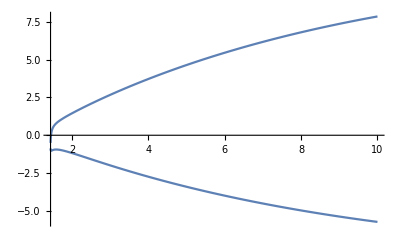

```mathematica
Plot[Rsol[r]//ReIm, {r,1.44,10}]
```

Comparison of Vector Field

```mathematica
TeuInterEnv`AdownNorm[2,2,2,2]
```

{-0.00297379,-0.00349691,0.00191785,0.0156192}

Comparison of EM Projections

```mathematica
TeuInterEnv`Tdowndown[2,2,2,2]
```

{{3.13879×10^-6,2.52493×10^-6,-7.82321×10^-7,-8.65037×10^-6},{2.52493×10^-6,-0.0000407638,0.000011431,-0.0000134078},{-7.82321×10^-7,0.000011431,0.000014501,4.31054×10^-6},{-8.65037×10^-6,-0.0000134078,4.31054×10^-6,0.0000400939}}

Comparison of EM Projections

```mathematica
With[{T=6, R=1},
Column[{
Row[{"TnnInter: \n\t"<>ToString[TnnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TnnInter]: \n\t"<>ToString[Derivative[1,0][TnnInter][T,R], InputForm]}],
Row[{"TmnInter: \n\t"<>ToString[TmnInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmnInter]: \n\t"<>ToString[Derivative[1,0][TmnInter][T,R], InputForm]}],
Row[{"TmmInter: \n\t"<>ToString[TmmInter[T,R], InputForm], Spacer[20], "\nDerivative[1,0][TmmInter]: \n\t"<>ToString[Derivative[1,0][TmmInter][T,R], InputForm]}]
}]
]
```

Comparison of Teukolsky Source Term

```mathematica
TeukolskyTintegrandExpl[20,1]
```

Comparison of SWSH

```mathematica
PrivateTeukolsky`SWSHS[2][1]
```

Comparison of Teukolsky integrand

```mathematica
teukint = {r,θ}|->TeukolskyTintegrandExpl[r,θ]*Sin[θ]*PrivateTeukolsky`SWSHS[2][θ];
Plot[teukint[r,1]//ReIm, {r,1.45,20}]
```

Comparison of Tlmω

```mathematica
Tlmω[2][3.86]
Tlmω[2]
Plot[Tlmω[2][r]//ReIm, {r,1.44,100}]
```

Comparison of Renormalized angular momentum

```mathematica
TeuInterEnv`νsolIn[2,2][2*TeuInterEnv`wr]//Evaluate
RenormalizedAngularMomentum[-2,2,2,0.9`20.,SetPrecision[4*TeuInterEnv`wr,64],Method->"Monodromy"]
```

Comparison of Homogeneous solution of MST

```mathematica
With[{TeuInterEnv`spinin=0.9,TeuInterEnv`wr=0.2836323604304887114412526546297144404`25.150514992000527,TeuInterEnv`rstop = 400},
Off[Power::infy];
MSTgRoots[TeuInterEnv`spinin,-2,2,2,2];
νsol[w_]:=nufullBHPT[w];
MSTSolution[TeuInterEnv`spinin,νsol[2*TeuInterEnv`wr],2*TeuInterEnv`wr,AlmSWSH[2*TeuInterEnv`wr], -2,2,2,TeuInterEnv`rstop];
rsol22 = MSTformalism`Rnumerical;
On[Power::infy];
]
```

Comparison of Z_lmω integrand

```mathematica
tlmw = TeuInterEnv`Tlmω[2];
Rin = {TeuInterEnv`r}|->TeuInterEnv`RinSet[2,2]//Evaluate;
integrand = {r}|->tlmw[r]*Rin[r]/((r^2-2*r+(0.9)^2)^2);
Plot[integrand[r]//Abs, {r,1.45,100}];
integrand[3.86]
```

Comparison of incoming amplitude

```mathematica
TeuInterEnv`BincSet[2,2]
```

Comparison of Z_lmω

```mathematica
integration = NIntegrate[integrand[rr],{rr,2.44,TeuInterEnv`rstop},MaxRecursion->50,WorkingPrecision->10]
zinf = integration/(2 * I * 2*TeuInterEnv`wr * TeuInterEnv`BincSet[2,2])
```